## Problem 1

```mathematica
z=x-W*t;
```

```mathematica
B[x_,t_]={0,u[z],v[z]};
```

```mathematica
e1= {1,0,0};
```

```mathematica
D[B[x,t],t]+D[(u[x-W*t]^2+v[x-W*t]^2)*B[x,t],x]+γ*Cross[e1,{0,B0,0}]*Dot[e1,Cross[D[B[x,t],x],{0,B0,0}]]+Cross[e1,D[B[x,t],{x,2}]]//FullSimplify
```

{0,(-W+3 u[-t W+x]^2+v[-t W+x]^2) u'[-t W+x]+2 u[-t W+x] v[-t W+x] v'[-t W+x]-v''[-t W+x],2 u[-t W+x] v[-t W+x] u'[-t W+x]+u[-t W+x]^2 v'[-t W+x]-(W+B0^2 γ-3 v[-t W+x]^2) v'[-t W+x]+u''[-t W+x]}

### Part c

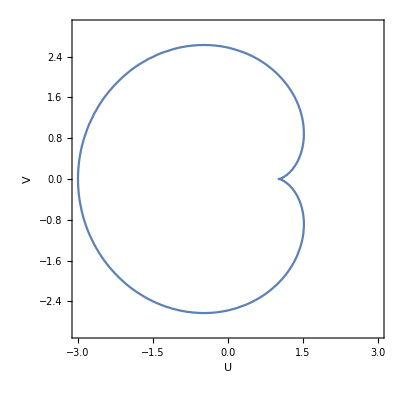

```mathematica
γ=1/10; W0=3;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->""]
```

We observe a single loop corresponding to a single soliton in each U and V.

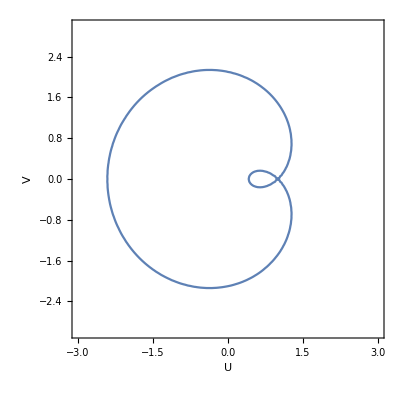

```mathematica
W0=2;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->""]
```

We observe an inner and an outer loop, meaning that we have two pairs of solitons in U and V.

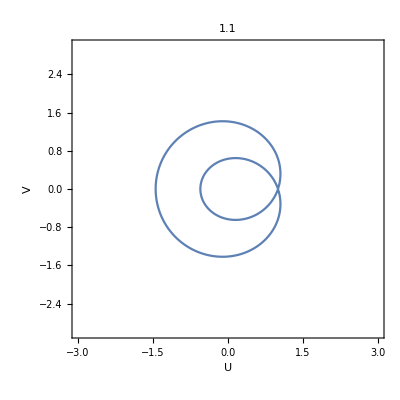

```mathematica
W0=1.1;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->"1.1",PlotPoints->100]
```

We again observe two loops, so we again have two pairs of solitons.

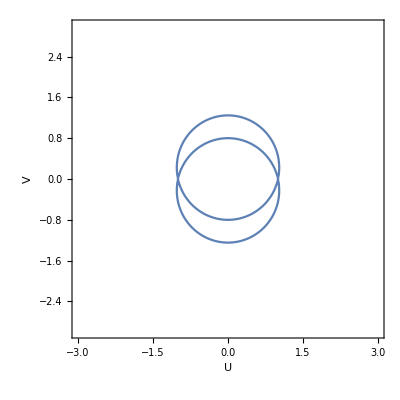

```mathematica
W0=1;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->"",PlotPoints->100]
```

Here, we have two interlocking circles. This is heteroclinic, so we actually have no solitons due to the fact that U and V are coupled.

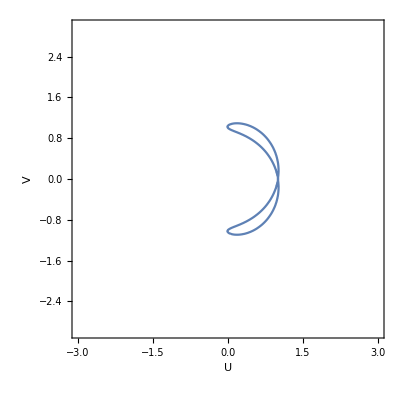

```mathematica
W0=0.95;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->"",PlotPoints->100]
```

Now, we again observe two pairs of solitons in U and V; however, the solitons in U are actually the same (so there’s really only one in U), and the solitons in V are reflections of each other.

```mathematica
W0=0.9;ContourPlot[3/4-W0/2==-U^2V^2/2-U^4/4+W0*U^2/2-(W0-1)*U-V^4/4+(W0+γ)*V^2/2,{U,-3,3},{V,-3,3},Axes->True,AxesLabel->Automatic,PlotLabel->""]
```

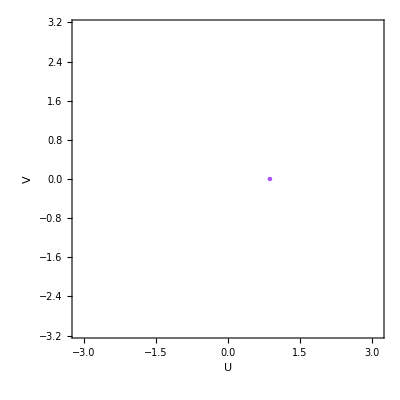

We only have the singular point here which Mathematica does not plot. Using the drawing tool, we plot it manually. Of course, this does not lead to any solitons.

## Problem 4

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
fn1=u[x,t]; f0=u[x,t]^2/2; f1=u[x,t]^3/6-D[u[x,t],x]^2/2; f2=u[x,t]^4/24-u[x,t]*D[u[x,t],x]^2/2+3*D[u[x,t],{x,2}]^2/10;
```

This function computes the insides of the integral of the Poisson bracket.

```mathematica
intpois[f_,g_]:=VariationalD[f,u[x,t],{x,t}]*D[VariationalD[g,u[x,t],{x,t}],x]
```

If this function returns zero, the integrals of the functions passed in are in involution.

```mathematica
involu[f_,g_]:=VariationalD[intpois[f,g],u[x,t],{x,t}]
```

```mathematica
testfuncs={{fn1,f0},{fn1,f1},{fn1,f2},{f0,f1},{f0,f2},{f1,f2}};
```

Here, we apply our involution checker to all necessary combinations and observe that they are all zero.

```mathematica
MapApply[involu,testfuncs]
```

{0,0,0,0,0,0}

## Problem 5

We compute the variational derivative of  so that we can see which coefficients will make it zero.

```mathematica
f=a1*u[x,t]^4+a2*u[x,t]*D[u[x,t],x]^2+a3*D[u[x,t],{x,2}]^2;
```

```mathematica
enforcekdv = {D[u[x,t],t]->-u[x,t]*D[u[x,t],x]-D[u[x,t],{x,3}],D[u[x,t],{x,1},t]->D[-u[x,t]*D[u[x,t],x]-D[u[x,t],{x,3}],x],D[u[x,t],{x,2},t]->D[-u[x,t]*D[u[x,t],x]-D[u[x,t],{x,3}],{x,2}]};
```

```mathematica
ft=D[f,t]/.enforcekdv;
```

```mathematica
VariationalD[ft,u[x,t],{x,t}]
```

VariationalD[4 a1 u[x,t]^3 (-u[x,t] u^(1,0)[x,t]-u^(3,0)[x,t])+a2 (u^(1,0)[x,t])^2 (-u[x,t] u^(1,0)[x,t]-u^(3,0)[x,t])+2 a2 u[x,t] u^(1,0)[x,t] (-(u^(1,0)[x,t])^2-u[x,t] u^(2,0)[x,t]-u^(4,0)[x,t])+2 a3 u^(2,0)[x,t] (-3 u^(1,0)[x,t] u^(2,0)[x,t]-u[x,t] u^(3,0)[x,t]-u^(5,0)[x,t]),u[x,t],{x,t}]

## Problem 6

```mathematica
Clear[v]
```

```mathematica
B0inv[v_]:=Integrate[v,x]
```

```mathematica
B1[v_]:=D[v,{x,3}]+(u[x,t]*D[v,x]+D[u[x,t]*v,x])/3
```

```mathematica
R[v_]:=B1[B0inv[v]]
```

Here, we apply our operator to an arbitrary function.

```mathematica
R[v[x,t]]
```

1/3 (2 u[x,t] v[x,t]+(∫v[x,t]ⅆx) u^(1,0)[x,t])+v^(2,0)[x,t]

Applying the operator once gives the first KdV flow.

```mathematica
kdv1=R[D[u[x,t],x]]
```

u[x,t] u^(1,0)[x,t]+u^(3,0)[x,t]

Applying it again gives the second KdV flow.

```mathematica
kdv2=R[kdv1]//Simplify
```

5/6 u[x,t]^2 u^(1,0)[x,t]+10/3 u^(1,0)[x,t] u^(2,0)[x,t]+5/3 u[x,t] u^(3,0)[x,t]+u^(5,0)[x,t]

Applying it once more gives the third KdV flow.

```mathematica
kdv3=R[kdv2]//Simplify
```

35/54 u[x,t]^3 u^(1,0)[x,t]+35/18 (u^(1,0)[x,t])^3+35/18 u[x,t]^2 u^(3,0)[x,t]+35/3 u^(2,0)[x,t] u^(3,0)[x,t]+7 u^(1,0)[x,t] u^(4,0)[x,t]+7/9 u[x,t] (10 u^(1,0)[x,t] u^(2,0)[x,t]+3 u^(5,0)[x,t])+u^(7,0)[x,t]

## Problem 7

```mathematica
Clear[U]
```

```mathematica
U[x_]=2*D[Log[1+Exp[k*x+α]],{x,2}];
```

Here, we solve for  in terms of  so that we have a soliton solution.

```mathematica
Solve[6U[x]*U'[x]+U'''[x]+c0*U'[x]==0,c0]//Simplify
```

{{c0→-k^2}}

```mathematica
u[x_,t1_,t2_,t3_]:=U[x]/.α->α[t1,t2,t3]
```

Plugging  into each KdV equation gives clear conditions on the time derivatives of  which guarantee a solution.

```mathematica
Solve[D[u[x,t1,t2,t3],t1]==6*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]+D[u[x,t1,t2,t3],{x,3}],D[α[t1,t2,t3],t1]]//Simplify
```

{{α^(1,0,0)[t1,t2,t3]→k^3}}

```mathematica
Solve[D[u[x,t1,t2,t3],t2]==30*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],x]+20*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}]+10*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,3}]+D[u[x,t1,t2,t3],{x,5}],D[α[t1,t2,t3],t2]]//Simplify
```

{{α^(0,1,0)[t1,t2,t3]→k^5}}

```mathematica
Solve[D[u[x,t1,t2,t3],t3]==140*u[x,t1,t2,t3]^3*D[u[x,t1,t2,t3],x]+70*D[u[x,t1,t2,t3],x]^3+280*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}]+70*D[u[x,t1,t2,t3],{x,2}]*D[u[x,t1,t2,t3],{x,3}]+70*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],{x,3}]+42*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,4}]+14*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,5}]+D[u[x,t1,t2,t3],{x,7}],D[α[t1,t2,t3],t3]]//Simplify
```

{{α^(0,0,1)[t1,t2,t3]→k^7}}

## Problem 8

```mathematica
Clear[U,u]
```

```mathematica
U[x_]=2*D[Log[1+Exp[k1*x+α]+Exp[k2*x+β]+((k1-k2)/(k1+k2))^2*Exp[k1*x+α+k2*x+β]],{x,2}];
```

```mathematica
vlongterm=30*U[x]^2*U'[x]+20*U'[x]*U''[x]+10*U[x]*U'''[x]+U'''''[x]+c1*(6*U[x]*U'[x]+U'''[x])+c0*U'[x]//Simplify
```

-((2 (k1+k2)^2 (-ⅇ^(k1 x+α) k1^11+ⅇ^(2 (k1 x+α)) k1^11-3 ⅇ^(k1 x+k2 x+α+β) k1^11+3 ⅇ^(2 (k1 x+k2 x+α+β)) k1^11+3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^11-3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^11-ⅇ^(k1 x+3 k2 x+α+3 β) k1^11+ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^11-4 ⅇ^(k1 x+α) k1^10 k2+4 ⅇ^(2 (k1 x+α)) k1^10 k2-8 ⅇ^(k1 x+k2 x+α+β) k1^10 k2-4 ⅇ^(2 (k1 x+k2 x+α+β)) k1^10 k2+4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^10 k2-4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^10 k2-4 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^10 k2-6 ⅇ^(k1 x+α) k1^9 k2^2+6 ⅇ^(2 (k1 x+α)) k1^9 k2^2-2 ⅇ^(k1 x+k2 x+α+β) k1^9 k2^2-6 ⅇ^(2 (k1 x+k2 x+α+β)) k1^9 k2^2-6 ⅇ^(2 k1 x+k2 x+2 α+β) k1^9 k2^2+6 ⅇ^(k1 x+2 k2 x+α+2 β) k1^9 k2^2+2 ⅇ^(k1 x+3 k2 x+α+3 β) k1^9 k2^2+6 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^9 k2^2-4 ⅇ^(k1 x+α) k1^8 k2^3+4 ⅇ^(2 (k1 x+α)) k1^8 k2^3+12 ⅇ^(k1 x+k2 x+α+β) k1^8 k2^3+8 ⅇ^(2 (k1 x+k2 x+α+β)) k1^8 k2^3-8 ⅇ^(2 k1 x+k2 x+2 α+β) k1^8 k2^3+8 ⅇ^(k1 x+2 k2 x+α+2 β) k1^8 k2^3-4 ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^8 k2^3-ⅇ^(k1 x+α) k1^7 k2^4+ⅇ^(2 (k1 x+α)) k1^7 k2^4+13 ⅇ^(k1 x+k2 x+α+β) k1^7 k2^4+3 ⅇ^(2 (k1 x+k2 x+α+β)) k1^7 k2^4+3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^7 k2^4-3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^7 k2^4-ⅇ^(k1 x+3 k2 x+α+3 β) k1^7 k2^4+ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^7 k2^4+4 ⅇ^(k1 x+k2 x+α+β) k1^6 k2^5-4 ⅇ^(2 (k1 x+k2 x+α+β)) k1^6 k2^5+4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^6 k2^5-4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^6 k2^5+4 ⅇ^(k1 x+k2 x+α+β) k1^5 k2^6-4 ⅇ^(2 (k1 x+k2 x+α+β)) k1^5 k2^6-4 ⅇ^(2 k1 x+k2 x+2 α+β) k1^5 k2^6+4 ⅇ^(k1 x+2 k2 x+α+2 β) k1^5 k2^6-ⅇ^(k2 x+β) k1^4 k2^7+ⅇ^(2 (k2 x+β)) k1^4 k2^7+13 ⅇ^(k1 x+k2 x+α+β) k1^4 k2^7+3 ⅇ^(2 (k1 x+k2 x+α+β)) k1^4 k2^7-3 ⅇ^(2 k1 x+k2 x+2 α+β) k1^4 k2^7-ⅇ^(3 k1 x+k2 x+3 α+β) k1^4 k2^7+3 ⅇ^(k1 x+2 k2 x+α+2 β) k1^4 k2^7+ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^4 k2^7-4 ⅇ^(k2 x+β) k1^3 k2^8+4 ⅇ^(2 (k2 x+β)) k1^3 k2^8+12 ⅇ^(k1 x+k2 x+α+β) k1^3 k2^8+8 ⅇ^(2 (k1 x+k2 x+α+β)) k1^3 k2^8+8 ⅇ^(2 k1 x+k2 x+2 α+β) k1^3 k2^8-8 ⅇ^(k1 x+2 k2 x+α+2 β) k1^3 k2^8-4 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^3 k2^8-6 ⅇ^(k2 x+β) k1^2 k2^9+6 ⅇ^(2 (k2 x+β)) k1^2 k2^9-2 ⅇ^(k1 x+k2 x+α+β) k1^2 k2^9-6 ⅇ^(2 (k1 x+k2 x+α+β)) k1^2 k2^9+6 ⅇ^(2 k1 x+k2 x+2 α+β) k1^2 k2^9+2 ⅇ^(3 k1 x+k2 x+3 α+β) k1^2 k2^9-6 ⅇ^(k1 x+2 k2 x+α+2 β) k1^2 k2^9+6 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1^2 k2^9-4 ⅇ^(k2 x+β) k1 k2^10+4 ⅇ^(2 (k2 x+β)) k1 k2^10-8 ⅇ^(k1 x+k2 x+α+β) k1 k2^10-4 ⅇ^(2 (k1 x+k2 x+α+β)) k1 k2^10-4 ⅇ^(2 k1 x+k2 x+2 α+β) k1 k2^10+4 ⅇ^(k1 x+2 k2 x+α+2 β) k1 k2^10-4 ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k1 k2^10-ⅇ^(k2 x+β) k2^11+ⅇ^(2 (k2 x+β)) k2^11-3 ⅇ^(k1 x+k2 x+α+β) k2^11+3 ⅇ^(2 (k1 x+k2 x+α+β)) k2^11-3 ⅇ^(2 k1 x+k2 x+2 α+β) k2^11-ⅇ^(3 k1 x+k2 x+3 α+β) k2^11+3 ⅇ^(k1 x+2 k2 x+α+2 β) k2^11+ⅇ^(3 k1 x+2 k2 x+3 α+2 β) k2^11+c0 (ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^3 (k1-k2)^4+ⅇ^(3 k1 x+2 k2 x+3 α+2 β) (k1-k2)^4 k2^3-ⅇ^(k1 x+α) k1^3 (k1+k2)^4+ⅇ^(2 (k1 x+α)) k1^3 (k1+k2)^4-ⅇ^(k2 x+β) k2^3 (k1+k2)^4+ⅇ^(2 (k2 x+β)) k2^3 (k1+k2)^4-ⅇ^(k1 x+3 k2 x+α+3 β) k1^3 (k1^2-k2^2)^2-ⅇ^(3 k1 x+k2 x+3 α+β) k2^3 (k1^2-k2^2)^2+ⅇ^(2 (k1 x+k2 x+α+β)) (k1-k2)^2 (k1+k2)^3 (3 k1^2-7 k1 k2+3 k2^2)-ⅇ^(k1 x+k2 x+α+β) (k1+k2)^5 (3 k1^2-7 k1 k2+3 k2^2)+ⅇ^(2 k1 x+k2 x+2 α+β) (k1-k2)^3 (k1+k2)^2 (3 k1^2+7 k1 k2+3 k2^2)-ⅇ^(k1 x+2 k2 x+α+2 β) (k1-k2)^3 (k1+k2)^2 (3 k1^2+7 k1 k2+3 k2^2))+c1 (ⅇ^(2 k1 x+3 k2 x+2 α+3 β) k1^5 (k1-k2)^4+ⅇ^(3 k1 x+2 k2 x+3 α+2 β) (k1-k2)^4 k2^5-ⅇ^(k1 x+α) k1^5 (k1+k2)^4+ⅇ^(2 (k1 x+α)) k1^5 (k1+k2)^4-ⅇ^(k2 x+β) k2^5 (k1+k2)^4+ⅇ^(2 (k2 x+β)) k2^5 (k1+k2)^4-ⅇ^(k1 x+3 k2 x+α+3 β) k1^5 (k1^2-k2^2)^2-ⅇ^(3 k1 x+k2 x+3 α+β) k2^5 (k1^2-k2^2)^2+ⅇ^(2 (k1 x+k2 x+α+β)) (k1-k2)^2 (k1+k2)^3 (3 k1^4-7 k1^3 k2+7 k1^2 k2^2-7 k1 k2^3+3 k2^4)-ⅇ^(k1 x+k2 x+α+β) (k1+k2)^5 (3 k1^4-7 k1^3 k2+7 k1^2 k2^2-7 k1 k2^3+3 k2^4)+ⅇ^(2 k1 x+k2 x+2 α+β) (k1-k2)^3 (k1+k2)^2 (3 k1^4+7 k1^3 k2+7 k1^2 k2^2+7 k1 k2^3+3 k2^4)-ⅇ^(k1 x+2 k2 x+α+2 β) (k1-k2)^3 (k1+k2)^2 (3 k1^4+7 k1^3 k2+7 k1^2 k2^2+7 k1 k2^3+3 k2^4))))/((1+ⅇ^(k1 x+α)) (1+ⅇ^(k2 x+β)) k1^2-2 (-1-ⅇ^(k1 x+α)-ⅇ^(k2 x+β)+ⅇ^(k1 x+k2 x+α+β)) k1 k2+(1+ⅇ^(k1 x+α)) (1+ⅇ^(k2 x+β)) k2^2)^3)

Here, we eliminate some terms which clearly don’t matter.

```mathematica
lilshorter=Numerator[vlongterm]/(2 (k1+k2)^2 );
```

Mathematica can’t solve the whole equation in a reasonable amount of time, so we pick 2 exponential terms (more or less at random) and equate their coefficients to zero. This ensures a 2 by 2 system for  which will hopefully produce a solution if we picked the right terms.

```mathematica
trythis=Coefficient[lilshorter,ⅇ^(k1 x+k2 x+α+β)];
```

```mathematica
anotherone=Coefficient[lilshorter,ⅇ^(2 k1 x+3 k2 x+2 α+3 β)];
```

```mathematica
Solve[{trythis==0,anotherone==0},{c0,c1}]
```

{{c0→k1^2 k2^2,c1→-k1^2-k2^2}}

We appear to have a solution, so let’s check if this actually solves the whole system.

```mathematica
check=vlongterm/.{c0->k1^2 k2^2,c1->-k1^2-k2^2}//Simplify
```

0

```mathematica
u[x_,t1_,t2_,t3_]:=U[x]/.{α->α[t1,t2,t3],β->β[t1,t2,t3]}
```

```mathematica
longterm1=D[u[x,t1,t2,t3],t1]-6*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]-D[u[x,t1,t2,t3],{x,3}]//Simplify
```

(2 (k1+k2)^2 (-ⅇ^(k1 x+α[t1,t2,t3]) k1^9+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^9-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^9+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^9+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^9-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^9-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^8 k2+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^8 k2-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^8 k2+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^8 k2-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^8 k2-6 ⅇ^(k1 x+α[t1,t2,t3]) k1^7 k2^2+6 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^7 k2^2-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^2-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^7 k2^2-6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^2+6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^7 k2^2+2 ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^2+6 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^2-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^6 k2^3+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^6 k2^3+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^3+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^6 k2^3-8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^3+8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 k2^3-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^6 k2^3-ⅇ^(k1 x+α[t1,t2,t3]) k1^5 k2^4+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^5 k2^4+17 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^4-ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^5 k2^4-ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^4+ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2^4-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^5 k2^4+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^5 k2^4-ⅇ^(k2 x+β[t1,t2,t3]) k1^4 k2^5+ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^4 k2^5+17 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^5-ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^4 k2^5+ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^5-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^5-ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^5+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^5-4 ⅇ^(k2 x+β[t1,t2,t3]) k1^3 k2^6+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^3 k2^6+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^6+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^3 k2^6+8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^6-8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^6-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^6-6 ⅇ^(k2 x+β[t1,t2,t3]) k1^2 k2^7+6 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^2 k2^7-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^7-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^2 k2^7+6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^7+2 ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^7-6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^7+6 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^7-4 ⅇ^(k2 x+β[t1,t2,t3]) k1 k2^8+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1 k2^8-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^8-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2^8-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^8+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^8-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^8-ⅇ^(k2 x+β[t1,t2,t3]) k2^9+ⅇ^(2 (k2 x+β[t1,t2,t3])) k2^9-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k2^9+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k2^9-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k2^9-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k2^9+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k2^9+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^9+ⅇ^α[t1,t2,t3] k1 (-ⅇ^(2 k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1 (k1-k2)^4+ⅇ^(k1 x) k1 (k1+k2)^4-ⅇ^(2 k1 x+α[t1,t2,t3]) k1 (k1+k2)^4+ⅇ^((k1+k2) x+β[t1,t2,t3]) (3 k1-4 k2) (k1+k2)^4+ⅇ^(k1 x+3 k2 x+3 β[t1,t2,t3]) k1 (k1^2-k2^2)^2-ⅇ^(α[t1,t2,t3]+2 ((k1+k2) x+β[t1,t2,t3])) (3 k1-4 k2) (k1^2-k2^2)^2-ⅇ^(2 k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2+ⅇ^(k1 x+2 k2 x+2 β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2) α^(1,0,0)[t1,t2,t3]+ⅇ^β[t1,t2,t3] k2 (-ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) (k1-k2)^4 k2-ⅇ^((k1+k2) x+α[t1,t2,t3]) (4 k1-3 k2) (k1+k2)^4+ⅇ^(k2 x) k2 (k1+k2)^4-ⅇ^(2 k2 x+β[t1,t2,t3]) k2 (k1+k2)^4+ⅇ^(2 (k1+k2) x+2 α[t1,t2,t3]+β[t1,t2,t3]) (4 k1-3 k2) (k1^2-k2^2)^2+ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]) k2 (k1^2-k2^2)^2+ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2-ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2) β^(1,0,0)[t1,t2,t3]))/((1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k1^2+2 (1+ⅇ^(k1 x+α[t1,t2,t3])+ⅇ^(k2 x+β[t1,t2,t3])-ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2+(1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k2^2)^3

```mathematica
shorterterm1=Numerator[longterm1]/(2 (k1+k2)^2 );
```

We employ the same strategy as before to get a system that Mathematica can solve in a reasonable amount of time.

```mathematica
eqn1=Coefficient[shorterterm1,ⅇ^(k2 x+β[t1,t2,t3])];
```

```mathematica
eqn2=Coefficient[shorterterm1,ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3])];
```

```mathematica
Solve[{eqn1==0,eqn2==0},{D[α[t1,t2,t3],t1],D[β[t1,t2,t3],t1]}]//Simplify
```

{{α^(1,0,0)[t1,t2,t3]→k1^3,β^(1,0,0)[t1,t2,t3]→k2^3}}

This appears to suggest that and . We plug this back in to verify that this does indeed work.

```mathematica
check1=longterm1/.{Derivative[1,0,0][α][t1,t2,t3]->k1^3,Derivative[1,0,0][β][t1,t2,t3]->k2^3}//Simplify
```

0

```mathematica
longterm2=D[u[x,t1,t2,t3],t2]-(30*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],x]+20*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}]+10*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,3}]+D[u[x,t1,t2,t3],{x,5}])//Simplify
```

(2 (k1+k2)^2 (-ⅇ^(k1 x+α[t1,t2,t3]) k1^11+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^11-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^11+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^11+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^11-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^11-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^10 k2+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^10 k2-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^10 k2+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^10 k2-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^10 k2-6 ⅇ^(k1 x+α[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^9 k2^2-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^2-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^9 k2^2-6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^9 k2^2+2 ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^2+6 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^2-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^8 k2^3+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^8 k2^3+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^3+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^8 k2^3-8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^3+8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^8 k2^3-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^8 k2^3-ⅇ^(k1 x+α[t1,t2,t3]) k1^7 k2^4+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^7 k2^4+13 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^4+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^7 k2^4+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^7 k2^4-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^7 k2^4-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^4+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^7 k2^4+4 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^5-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^6 k2^5+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^6 k2^5-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^6 k2^5+4 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^6-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^5 k2^6-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^6+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2^6-ⅇ^(k2 x+β[t1,t2,t3]) k1^4 k2^7+ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^4 k2^7+13 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^4 k2^7-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^7+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^7+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^7-4 ⅇ^(k2 x+β[t1,t2,t3]) k1^3 k2^8+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^3 k2^8+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^8+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^3 k2^8+8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^8-8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^8-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^8-6 ⅇ^(k2 x+β[t1,t2,t3]) k1^2 k2^9+6 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^2 k2^9-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^2 k2^9+6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9+2 ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^9-6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^9+6 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^9-4 ⅇ^(k2 x+β[t1,t2,t3]) k1 k2^10+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1 k2^10-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^10-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2^10-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^10+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^10-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^10-ⅇ^(k2 x+β[t1,t2,t3]) k2^11+ⅇ^(2 (k2 x+β[t1,t2,t3])) k2^11-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k2^11+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k2^11-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k2^11-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k2^11+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k2^11+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^11+ⅇ^α[t1,t2,t3] k1 (-ⅇ^(2 k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1 (k1-k2)^4+ⅇ^(k1 x) k1 (k1+k2)^4-ⅇ^(2 k1 x+α[t1,t2,t3]) k1 (k1+k2)^4+ⅇ^((k1+k2) x+β[t1,t2,t3]) (3 k1-4 k2) (k1+k2)^4+ⅇ^(k1 x+3 k2 x+3 β[t1,t2,t3]) k1 (k1^2-k2^2)^2-ⅇ^(α[t1,t2,t3]+2 ((k1+k2) x+β[t1,t2,t3])) (3 k1-4 k2) (k1^2-k2^2)^2-ⅇ^(2 k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2+ⅇ^(k1 x+2 k2 x+2 β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2) α^(0,1,0)[t1,t2,t3]+ⅇ^β[t1,t2,t3] k2 (-ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) (k1-k2)^4 k2-ⅇ^((k1+k2) x+α[t1,t2,t3]) (4 k1-3 k2) (k1+k2)^4+ⅇ^(k2 x) k2 (k1+k2)^4-ⅇ^(2 k2 x+β[t1,t2,t3]) k2 (k1+k2)^4+ⅇ^(2 (k1+k2) x+2 α[t1,t2,t3]+β[t1,t2,t3]) (4 k1-3 k2) (k1^2-k2^2)^2+ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]) k2 (k1^2-k2^2)^2+ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2-ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2) β^(0,1,0)[t1,t2,t3]))/((1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k1^2+2 (1+ⅇ^(k1 x+α[t1,t2,t3])+ⅇ^(k2 x+β[t1,t2,t3])-ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2+(1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k2^2)^3

```mathematica
shorterterm2=Numerator[longterm2]/(2 (k1+k2)^2 );
```

```mathematica
eqn1=Coefficient[shorterterm2,ⅇ^(k2 x+β[t1,t2,t3])];
```

```mathematica
eqn2=Coefficient[shorterterm2,ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3])];
```

```mathematica
Solve[{eqn1==0,eqn2==0},{D[α[t1,t2,t3],t2],D[β[t1,t2,t3],t2]}]//Simplify
```

{{α^(0,1,0)[t1,t2,t3]→k1^5,β^(0,1,0)[t1,t2,t3]→k2^5}}

This appears to give that and . We plug this back in to verify that this does indeed work.

```mathematica
check2=longterm2/.{Derivative[0,1,0][α][t1,t2,t3]->k1^5,Derivative[0,1,0][β][t1,t2,t3]->k2^5}//Simplify
```

0

```mathematica
longterm3=D[u[x,t1,t2,t3],t3]-(140*u[x,t1,t2,t3]^3*D[u[x,t1,t2,t3],x]+70*D[u[x,t1,t2,t3],x]^3+280*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,2}]+70*D[u[x,t1,t2,t3],{x,2}]*D[u[x,t1,t2,t3],{x,3}]+70*u[x,t1,t2,t3]^2*D[u[x,t1,t2,t3],{x,3}]+42*D[u[x,t1,t2,t3],x]*D[u[x,t1,t2,t3],{x,4}]+14*u[x,t1,t2,t3]*D[u[x,t1,t2,t3],{x,5}]+D[u[x,t1,t2,t3],{x,7}])//Simplify
```

(2 (k1+k2)^2 (-ⅇ^(k1 x+α[t1,t2,t3]) k1^13+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^13-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^13+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^13+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^13-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^13-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^13+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^13-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^12 k2+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^12 k2-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^12 k2-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^12 k2+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^12 k2-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^12 k2-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^12 k2-6 ⅇ^(k1 x+α[t1,t2,t3]) k1^11 k2^2+6 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^11 k2^2-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^11 k2^2-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^11 k2^2-6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^11 k2^2+6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^11 k2^2+2 ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11 k2^2+6 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^11 k2^2-4 ⅇ^(k1 x+α[t1,t2,t3]) k1^10 k2^3+4 ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^10 k2^3+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2^3+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^10 k2^3-8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^10 k2^3+8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^10 k2^3-4 ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^10 k2^3-ⅇ^(k1 x+α[t1,t2,t3]) k1^9 k2^4+ⅇ^(2 (k1 x+α[t1,t2,t3])) k1^9 k2^4+13 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^4+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^9 k2^4+3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^9 k2^4-3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^9 k2^4-ⅇ^(k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^4+ⅇ^(2 k1 x+3 k2 x+2 α[t1,t2,t3]+3 β[t1,t2,t3]) k1^9 k2^4+4 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^5-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^8 k2^5+4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^8 k2^5-4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^8 k2^5+4 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^8-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^5 k2^8-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^5 k2^8+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^5 k2^8-ⅇ^(k2 x+β[t1,t2,t3]) k1^4 k2^9+ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^4 k2^9+13 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^9+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^4 k2^9-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^9-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^4 k2^9+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^9+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^4 k2^9-4 ⅇ^(k2 x+β[t1,t2,t3]) k1^3 k2^10+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^3 k2^10+12 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^10+8 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^3 k2^10+8 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^3 k2^10-8 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^10-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^3 k2^10-6 ⅇ^(k2 x+β[t1,t2,t3]) k1^2 k2^11+6 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1^2 k2^11-2 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^11-6 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1^2 k2^11+6 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^11+2 ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k1^2 k2^11-6 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^11+6 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1^2 k2^11-4 ⅇ^(k2 x+β[t1,t2,t3]) k1 k2^12+4 ⅇ^(2 (k2 x+β[t1,t2,t3])) k1 k2^12-8 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^12-4 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2^12-4 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k1 k2^12+4 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^12-4 ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k1 k2^12-ⅇ^(k2 x+β[t1,t2,t3]) k2^13+ⅇ^(2 (k2 x+β[t1,t2,t3])) k2^13-3 ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3]) k2^13+3 ⅇ^(2 ((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k2^13-3 ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]+β[t1,t2,t3]) k2^13-ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) k2^13+3 ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+2 β[t1,t2,t3]) k2^13+ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+2 β[t1,t2,t3]) k2^13+ⅇ^α[t1,t2,t3] k1 (-ⅇ^(2 k1 x+3 k2 x+α[t1,t2,t3]+3 β[t1,t2,t3]) k1 (k1-k2)^4+ⅇ^(k1 x) k1 (k1+k2)^4-ⅇ^(2 k1 x+α[t1,t2,t3]) k1 (k1+k2)^4+ⅇ^((k1+k2) x+β[t1,t2,t3]) (3 k1-4 k2) (k1+k2)^4+ⅇ^(k1 x+3 k2 x+3 β[t1,t2,t3]) k1 (k1^2-k2^2)^2-ⅇ^(α[t1,t2,t3]+2 ((k1+k2) x+β[t1,t2,t3])) (3 k1-4 k2) (k1^2-k2^2)^2-ⅇ^(2 k1 x+k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2+ⅇ^(k1 x+2 k2 x+2 β[t1,t2,t3]) (3 k1+4 k2) (k1^2-k2^2)^2) α^(0,0,1)[t1,t2,t3]+ⅇ^β[t1,t2,t3] k2 (-ⅇ^(3 k1 x+2 k2 x+3 α[t1,t2,t3]+β[t1,t2,t3]) (k1-k2)^4 k2-ⅇ^((k1+k2) x+α[t1,t2,t3]) (4 k1-3 k2) (k1+k2)^4+ⅇ^(k2 x) k2 (k1+k2)^4-ⅇ^(2 k2 x+β[t1,t2,t3]) k2 (k1+k2)^4+ⅇ^(2 (k1+k2) x+2 α[t1,t2,t3]+β[t1,t2,t3]) (4 k1-3 k2) (k1^2-k2^2)^2+ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3]) k2 (k1^2-k2^2)^2+ⅇ^(2 k1 x+k2 x+2 α[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2-ⅇ^(k1 x+2 k2 x+α[t1,t2,t3]+β[t1,t2,t3]) (4 k1+3 k2) (k1^2-k2^2)^2) β^(0,0,1)[t1,t2,t3]))/((1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k1^2+2 (1+ⅇ^(k1 x+α[t1,t2,t3])+ⅇ^(k2 x+β[t1,t2,t3])-ⅇ^((k1+k2) x+α[t1,t2,t3]+β[t1,t2,t3])) k1 k2+(1+ⅇ^(k1 x+α[t1,t2,t3])) (1+ⅇ^(k2 x+β[t1,t2,t3])) k2^2)^3

```mathematica
shorterterm3=Numerator[longterm3]/(2 (k1+k2)^2 );
```

```mathematica
eqn1=Coefficient[shorterterm3,ⅇ^(k2 x+β[t1,t2,t3])];
```

```mathematica
eqn2=Coefficient[shorterterm3,ⅇ^(3 k1 x+k2 x+3 α[t1,t2,t3])];
```

```mathematica
Solve[{eqn1==0,eqn2==0},{D[α[t1,t2,t3],t3],D[β[t1,t2,t3],t3]}]//Simplify
```

{{α^(0,0,1)[t1,t2,t3]→k1^7,β^(0,0,1)[t1,t2,t3]→k2^7}}

This appears to give that and . We plug this back in to verify that this does indeed work.

```mathematica
check3=longterm3/.{Derivative[0,0,1][α][t1,t2,t3]->k1^7,Derivative[0,0,1][β][t1,t2,t3]->k2^7}//Simplify
```

0